# Ixn params

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
datahA={};
datawAX={};
databX={};
Do[

AppendTo[datahA,Import["../data_learned/ixn_params/hA_"<>IntegerString[iOpt,10,3]<>".txt","Table"][[1,1]]];

AppendTo[datawAX,Import["../data_learned/ixn_params/wAX_"<>IntegerString[iOpt,10,3]<>".txt","Table"][[1,1]]];

AppendTo[databX,Import["../data_learned/ixn_params/bX_"<>IntegerString[iOpt,10,3]<>".txt","Table"][[1,1]]];
,{iOpt,1,999,1}]
```

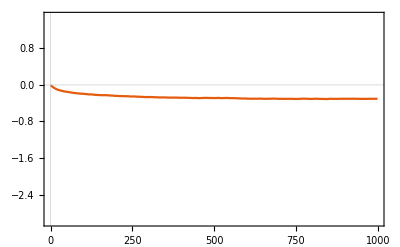
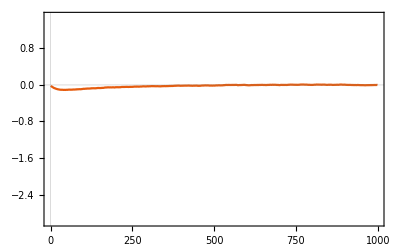
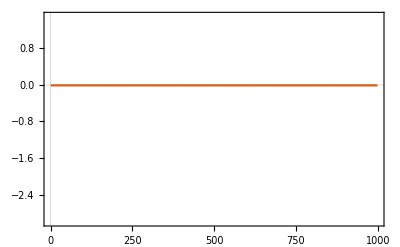

```mathematica
Row[{
ListLinePlot[datahA,PlotRange->{-3,1.5}],
ListLinePlot[datawAX,PlotRange->{-3,1.5}],
ListLinePlot[databX,PlotRange->{-3,1.5}]
}]
```